```mathematica
F[x_, y_] = Tan[x * y] - x^ 2
```

-x^2+Tan[x y]

```mathematica
G[x_, y_] = x + Log[y / 15]
```

x+Log[y/15]

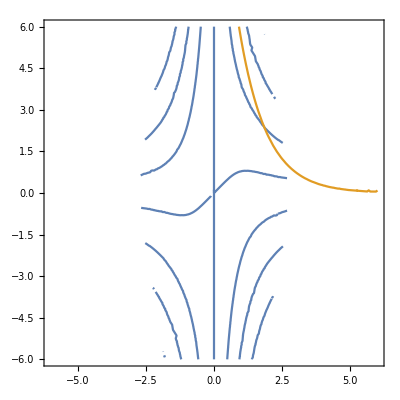

```mathematica
ContourPlot[{F[x, y] ==0, G[x, y]== 0}, {x, -6, 6}, {y, -6, 6}]
```

```mathematica
FindRoot[{Tan[x * y] - x^2 ==0, -1 *Log[y / 15] == x},{{x, 1}, {y, 2}}]
```

```mathematica
{x->1.8217890100280008,y->2.426042165586433}
```